```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

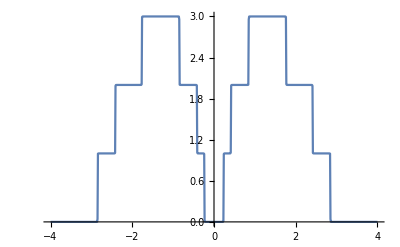

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
ϕ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
ϕ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
(*ϕ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*ϕ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}], μ8=RandomInteger[{1,7}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[7]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>3,3,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]*)
```

```mathematica
(*k714[ω_,ϵ1_]:=k714[ω,ϵ1]=Append[{},Table[ϕ14[ω,0.001,1,0,ϵ1],{i,100}]];
k713[ω_,ϵ1_]:=k713[ω,ϵ1]=Append[{},Table[ϕ13[ω,0.001,1,0,ϵ1],{i,100}]];
k712[ω_,ϵ1_]:=k712[ω,ϵ1]=Append[{},Table[ϕ12[ω,0.001,1,0,ϵ1],{i,100}]];
k711[ω_,ϵ1_]:=k711[ω,ϵ1]=Append[{},Table[ϕ11[ω,0.001,1,0,ϵ1],{i,100}]];
k710[ω_,ϵ1_]:=k710[ω,ϵ1]=Append[{},Table[ϕ10[ω,0.001,1,0,ϵ1],{i,100}]];
k79[ω_,ϵ1_]:=k79[ω,ϵ1]=Append[{},Table[ϕ9[ω,0.001,1,0,ϵ1],{i,100}]];
k78[ω_,ϵ1_]:=k78[ω,ϵ1]=Append[{},Table[ϕ8[ω,0.001,1,0,ϵ1],{i,100}]];,Mean[k78[ω,ϵ1]],Mean[k79[ω,ϵ1]],Mean[k710[ω,ϵ1]],Mean[k711[ω,ϵ1]],Mean[k713[ω,ϵ1]],Mean[k714[ω,ϵ1]]*)
```

```mathematica
k77[ω_,ϵ1_]:=k77[ω,ϵ1]=Append[{},Table[ϕ7[ω,0.001,1,0,ϵ1],{i,100}]];
k76[ω_,ϵ1_]:=k76[ω,ϵ1]=Append[{},Table[ϕ6[ω,0.001,1,0,ϵ1],{i,100}]];
k75[ω_,ϵ1_]:=k75[ω,ϵ1]=Append[{},Table[ϕ5[ω,0.001,1,0,ϵ1],{i,100}]];
k74[ω_,ϵ1_]:=k74[ω,ϵ1]=Append[{},Table[ϕ4[ω,0.001,1,0,ϵ1],{i,100}]];
k73[ω_,ϵ1_]:=k73[ω,ϵ1]=Append[{},Table[ϕ3[ω,0.001,1,0,ϵ1],{i,100}]];
k72[ω_,ϵ1_]:=k72[ω,ϵ1]=Append[{},Table[ϕ2[ω,0.001,1,0,ϵ1],{i,100}]];
k71[ω_,ϵ1_]:=k71[ω,ϵ1]=Append[{},Table[ϕ1[ω,0.001,1,0,ϵ1],{i,100}]]
```

```mathematica
ρ7[ω_,ϵ1_]:=Join[Mean[k71[ω,ϵ1]],Mean[k72[ω,ϵ1]],Mean[k73[ω,ϵ1]],Mean[k74[ω,ϵ1]],Mean[k75[ω,ϵ1]],Mean[k76[ω,ϵ1]],Mean[k77[ω,ϵ1]]]
```

```mathematica
Mean[ρ7[0.5,0.5]]
```

1.50282

```mathematica
Export["7imp5.csv",Table[{ω,Mean[ρ7[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

7imp5.csv

```mathematica
Export["7imp4.csv",Table[{ω,Mean[ρ7[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

7imp4.csv

```mathematica
Export["7imp6.csv",Table[{ω,Mean[ρ7[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

7imp6.csv

```mathematica
Export["7imp7.csv",Table[{ω,Mean[ρ7[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

7imp7.csv

```mathematica
Export["7imp8.csv",Table[{ω,Mean[ρ7[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

7imp8.csv

```mathematica
Export["7imp9.csv",Table[{ω,Mean[ρ7[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

7imp9.csv

```mathematica
Export["7imp1.csv",Table[{ω,Mean[ρ7[ω,1]]},{ω,Range[0,4,0.01]}]]
```

7imp1.csv